Gamma

22.6068

k

0.874263

Censored CDF

0

0

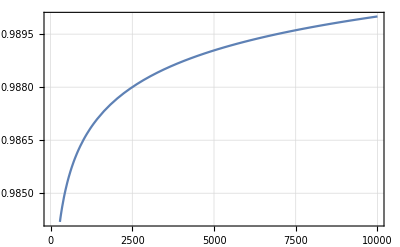

Piecewise[{{0.222491/((1+1.00596/(1/x)^0.0442344)^6 x^0.955766), x≥0}, {0, True}}]

CensoredDistribution[{0,10000},ParetoDistribution[0.874263,5,22.6068,0]]

Censored...

-Graphics-

```mathematica
GetParetoGamma[alpha_?NumericQ,pHigh_?NumericQ, pLow_?NumericQ, qHigh_?NumericQ, qLow_?NumericQ]:=Module[{q,sol, gamma, qVal},
qVal = qHigh/qLow;
q = (Quantile[ParetoDistribution[1,alpha,gamma,0],pHigh] / Quantile[ParetoDistribution[1,alpha,gamma,0],pLow]);
(* Print["q = ", q]; *)
Off[NSolve::ifun];
sol=NSolve[q==qVal, gamma];
(* On[NSolve::ifun]; *)
(* Print["sol = ", sol]; *)
Return[gamma /. sol[[1]]];
];

GetParetoK[alpha_?NumericQ,pHigh_?NumericQ, pLow_?NumericQ, qHigh_?NumericQ, qLow_?NumericQ]:=Module[{gamma, sol, qL, k},
gamma = GetParetoGamma[alpha,pHigh, pLow, qHigh, qLow];
qL= Quantile[ParetoDistribution[k,alpha,gamma,0],pLow];
sol=NSolve[qL==qLow , k];
(* Print["sol = ", sol]; *)
Return[k /. sol[[1]]];
];

alphaVal = 5;
pHighVal = 0.99;
pLowVal = 0.95;
qHighVal = 10^4;
qLowVal = 10^-2;

Print["Gamma"];
gammaVal = GetParetoGamma[alphaVal,pHighVal,pLowVal, qHighVal, qLowVal]

Print["k"];
kVal = GetParetoK[alphaVal,pHighVal,pLowVal, qHighVal, qLowVal]

Print["Censored CDF"];
CensoredCDF[x_?NumericQ]:=Module[{retVal},
retVal = CDF[CensoredDistribution[{0,qHighVal},ParetoDistribution[kVal,alphaVal]],x];
Return[retVal];
];

CensoredCDF[0.01]
CensoredCDF[0.5]


Plot[CDF[ParetoDistribution[kVal,alphaVal,gammaVal, 0],x],{x,0,qHighVal}, Frame->True, GridLines->Automatic]

PDF[ParetoDistribution[kVal,alphaVal,gammaVal, 0],x]
CensoredDistribution[{0,qHighVal},ParetoDistribution[kVal,alphaVal,gammaVal, 0]]
(*
Print["q95S"];
q95S=FullSimplify[Quantile[CensoredDistribution[{0,LL},ParetoDistribution[1,α,0]],95/100], α > 0]
q95S1=FullSimplify[Quantile[CensoredDistribution[{0,qHighVal},ParetoDistribution[kVal,alphaVal,gammaVal, 0]],95/100]]
*)

(* PDF[CensoredDistribution[{0,qHighVal},ParetoDistribution[kVal,alphaVal,gammaVal, 0]],x] *)

Print["Censored..."];
Plot[CDF[CensoredDistribution[{0,20000},ParetoDistribution[kVal,alphaVal,gammaVal, 0]],x],{x,0,qHighVal}, Frame->True, GridLines->Automatic]
```